## Nonlinear Pose Tracking Controller for Bar Tethered to Two Aerial Vehicles with Bounded Linear and Angular Accelerations

# Notation

```mathematica
(*Orthogonal Projection Operator*)
OP[x_]:=IdentityMatrix[3]-KroneckerProduct[x, x]
(*Skew symmetric matrix*)
Skew[ω_]:={{0,-ω[[3]],ω[[2]]},{ω[[3]],0,-ω[[1]]},{-ω[[2]],ω[[1]],0}}
Unskew[x_]:={x[[3]][[2]],x[[1]][[3]],x[[2]][[1]]}
(*Unskew[Skew[{aa,bb,cc}]]//MatrixForm*)
```

```mathematica
(*Parametrization of unit vector with psi and theta angle*)
(*uv1[{0,0}] = e1*)
uv1[θ_]:={Cos[θ[[2]]]Cos[θ[[1]]],Cos[θ[[2]]]Sin[θ[[1]]],-Sin[θ[[2]]]}
(*uv3[{0,0}] = e3*)
uv3[θ_]:={Cos[θ[[2]]] Sin[θ[[1]]],Sin[θ[[2]]],Cos[θ[[1]]] Cos[θ[[2]]]}

Duv1[θ_,ω_]:=(D[uv1[{θ1,θ2}],{{θ1,θ2}}].ω)/.Thread[{θ1,θ2}-> θ]
Duv3[θ_,ω_]:=(D[uv3[{θ1,θ2}],{{θ1,θ2}}].ω)/.Thread[{θ1,θ2}-> θ]

(*just checking orthogonality*)
(*uv1[{ψ,θ}].Duv1[{ψ,θ},{ωψ,ωθ}]//Simplify*)
(*uv3[{ψ,θ}].Duv3[{ψ,θ},{ωψ,ωθ}]//Simplify*)
```

# Modeling and Problem Statement

## State and input names (these are dummy names)

```mathematica
(*kinematic state*)
p={px,py,pz};
n={nx,ny,nz};
P1={p1x,p1y,p1z};
P2={p2x,p2y,p2z};
zk=Join[p,n,P1,P2];

(*dynamic state*)
v={vx,vy,vz};
ω={ωx,ωy,ωz};
V1={v1x,v1y,v1z};
V2={v2x,v2y,v2z};
zd=Join[v,ω,V1,V2];
(*full state*)
z=Join[zk,zd];
(*input*)
u1={u1x,u1y,u1z};
u2={u2x,u2y,u2z};
u=Join[u1,u2];
```

## Physical constants

```mathematica
(*Set some random parameters*)
PhysicalConstants ={
gravity-> 9.81(*gravity*),
m -> 0.5(*bar's mass*),
J-> 0.04(*bar's moment of inertia*),
L1-> 0.5,L2-> 0.65,(*cables' lengths*)
m1-> 1.2,m2-> 1.5,(*uavs' masses*)
d1-> 0.45,d2-> -0.55(*distances between bar's center-of-mass and cable*)
};

(*for a 'uniform bar' -- with length |d1| + |d2| (which is not necessarily the case) -- moment of inertia is given by*)
1/12 m (Abs[d1]+Abs[d2])^2/.PhysicalConstants
```

0.0416667

## State space

```mathematica
ZSET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=
{
n.n-1,
((#.# - L1^2)&)[P1-(p+d1 n)],
((#.# - L2^2)&)[P2-(p+d2 n)],
n.ω,
(#1.#2 &)[P1-(p+d1 n),V1-(v+d1 Skew[ω].n)],
(#1.#2 &)[P2-(p+d2 n),V2-(v+d2 Skew[ω].n)]
};
```

## Tangent to state space

```mathematica
δp={δpx,δpy,δpz};δn={δnx,δny,δnz};δP1={δp1x,δp1y,δp1z};δP2={δp2x,δp2y,δp2z};
δv={δvx,δvy,δvz};δω={δωx,δωy,δωz};δV1={δv1x,δv1y,δv1z};δV2={δv2x,δv2y,δv2z};
TangentZSET[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},
{δpx_,δpy_,δpz_,δnx_,δny_,δnz_,δp1x_,δp1y_,δp1z_,δp2x_,δp2y_,δp2z_,δvx_,δvy_,δvz_,δωx_,δωy_,δωz_,δv1x_,δv1y_,δv1z_,δv2x_,δv2y_,δv2z_}
]={
n.δn,
(#1.#2 &)[P1-(p+d1 n),δP1-(δp+d1 δn)],
(#1.#2&)[P2-(p+d2 n),δP2-(δp+d2 δn)],
δn.ω+n.δω,
(#3.#2+#1.#4 &)[P1-(p+d1 n),V1-(v+d1 Skew[ω].n),δP1-(δp+d1 δn),δV1-(δv+d1 Skew[δω].n+d1 Skew[ω].δn)],
(#3.#2+#1.#4 &)[P2-(p+d2 n),V2-(v+d2 Skew[ω].n),δP2-(δp+d2 δn),δV2-(δv+d2 Skew[δω].n+d2 Skew[ω].δn)]
};
```

## Function that generates a random element of state space

```mathematica
zl[l_]:=Join[
l[[1;;3]],
uv1[l[[4;;5]]],
l[[1;;3]]+d1 uv1[l[[4;;5]]]+L1 uv3[l[[6;;7]]],
l[[1;;3]]+d2 uv1[l[[4;;5]]]+L2 uv3[l[[8;;9]]],
l[[10;;12]],
Skew[uv1[l[[4;;5]]]].Duv1[l[[4;;5]],l[[13;;14]]],
l[[10;;12]]+d1 Duv1[l[[4;;5]],l[[13;;14]]]+L1 Duv3[l[[6;;7]],l[[15;;16]]],
l[[10;;12]]+d2 Duv1[l[[4;;5]],l[[13;;14]]]+L2 Duv3[l[[8;;9]],l[[17;;18]]]
]/.PhysicalConstants

zlR[]=zl[Join[ RandomReal[{-0.2,0.2},18]]];
(*zlR[]*)
(*Chop[ZSET[zl[Array[Subscript[y, #]&,24]]]]//Simplify*)
Chop[ZSET[zlR[]]/.PhysicalConstants]//Simplify
```

{0,0,0,0,0,0}

## function that takes an element in R24 and produces element in state space (projection onto state space)

```mathematica
D0uv=#/(√(#.#))&;
D1uv=OP[#1/(√(#1.#1))].(#2/(√(#1.#1)))&;

Proj[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=
Join[
p,
D0uv[n],
p+d1 D0uv[n]+L1 D0uv[P1-( p+d1 D0uv[n])],
p+d2 D0uv[n]+L2 D0uv[P2-( p+d2 D0uv[n])],
v,
OP[D0uv[n]].ω,
v+d1 Skew[ω].D0uv[n]+L1 D1uv[P1-( p+d1 D0uv[n]),V1-(v+d1 Skew[ω].D0uv[n])],
 v+d2 Skew[ω].D0uv[n]+L2 D1uv[P2-( p+d2 D0uv[n]),V2-(v+d2 Skew[ω].D0uv[n])]
];
Chop[(# -Proj[#])&[zlR[]]/.PhysicalConstants]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Vector field

```mathematica
(*cable unit vectors*)
nC1[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=(P1-(p+d1 n))/L1;
nC2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=(P2-(p+d2 n))/L2;

(*tensions on cables*)
MT[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=(DiagonalMatrix[{m/m1,m/m2}]+{{1,γ},{γ,1}}+(m d1 d2)/J{{d1/d2 δ1.δ1,δ1.δ2},{δ1.δ2,d2/d1 δ2.δ2}})/.{γ-> nC1[zk].nC2[zk],δ1-> Skew[n].nC1[zk],δ2-> Skew[n].nC2[zk]};

BB[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=
{
(nC1[zk].u1 m/m1+m/L1(#.#&)[V1-(v+d1 Skew[ω].n)]+ m d1 nC1[zk].n (#.#&)[ω]),
(nC2[zk].u2 m/m2+m/L2(#.#&)[V2-(v+d2 Skew[ω].n)]+ m d2 nC2[zk].n (#.#&)[ω])
};
Te[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Inverse[MT[zk]].BB[z,u];


a[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=1/m(T1 nC1[zk]+T2 nC2[zk]- m gravity {0,0,1})/.Thread[{T1,T2}-> Te[z,u]];
τB[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=1/J(Skew[d1 n].nC1[zk] T1 + Skew[d2 n].nC2[zk]T2)/.Thread[{T1,T2}-> Te[z,u]];
A1[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]= 1/m1(u1-T1 nC1[zk]- m1 gravity {0,0,1})/.Thread[{T1,T2}-> Te[z,u]];
A2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]= 1/m2(u2-T2 nC2[zk]- m2 gravity{0,0,1})/.Thread[{T1,T2}-> Te[z,u]];

Zk[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Join[
v,
Skew[ω].n,
V1,
V2
];

Zd[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Join[
a[z,u],
τB[z,u],
A1[z,u],
A2[z,u]
]/.PhysicalConstants;

Z [{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Join[Zk[z],Zd[z,u]];
(*Z[zlR[],u]/.Thread[u-> RandomReal[{-1,1},6]]/.PhysicalConstants*)

(*dynamics with zero input*)
ZdFree [{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Zd[z,{0,0,0,0,0,0}];
ZdFree[zlR[]]/.PhysicalConstants
```

{-0.00188977,0.0000707492,-9.79612,0.000263422,-0.0246369,-0.00114491,0.000467759,0.0000227679,-9.81401,0.000255716,-0.0000417974,-9.81142}

## Verify that vector field lies in tangent set

```mathematica
Chop[TangentZSET[z,Z[z,u]]/.PhysicalConstants/.Thread[z-> zlR[]]/.Thread[u-> RandomReal[{-1,1},6]]]
```

{0,0,0,0,0,0}

## Vector field is input affine

```mathematica
BlockDiagonalMatrix[b:{__?MatrixQ}]:=Module[{r,c,n=Length[b],i,j},{r,c}=Transpose[Dimensions/@b];
ArrayFlatten[Table[If[i==j,b[[i]],ConstantArray[0,{r[[i]],c[[j]]}]],{i,n},{j,n}]]]
```

kinematics ((ż)_k=F(z_k)z_d)

```mathematica
FS[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=BlockDiagonalMatrix[{IdentityMatrix[3],-Skew[n],IdentityMatrix[3],IdentityMatrix[3]}];
error[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Zk[z]-FS[zk].Join[v,ω,V1,V2];
Chop[error[zlR[]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

dynamics (B matrix)

```mathematica
T1U[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Join[({1,0}.Inverse[MT[zk]].{1,0} m/m1)nC1[zk],({1,0}.Inverse[MT[zk]].{0,1} m/m2)nC2[zk]];
T2U[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Join[({0,1}.Inverse[MT[zk]].{1,0} m/m1)nC1[zk],({0,1}.Inverse[MT[zk]].{0,1} m/m2)nC2[zk]];

BA[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=KroneckerProduct[nC1[zk]/m,T1U[zk]]+KroneckerProduct[nC2[zk]/m,T2U[zk]];
Bτ[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=KroneckerProduct[(Skew[d1 n].nC1[zk])/J,T1U[zk]]+KroneckerProduct[(Skew[d2 n].nC2[zk])/J,T2U[zk]];
BA1[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=1/m1 Join[IdentityMatrix[3],0IdentityMatrix[3],2]-KroneckerProduct[nC1[zk]/m1,T1U[zk]];
BA2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=1/m2 Join[0IdentityMatrix[3],IdentityMatrix[3],2]-KroneckerProduct[nC2[zk]/m2,T2U[zk]];


BU[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Join[BA[zk],Bτ[zk],BA1[zk],BA2[zk]];
```

## Confirm vector field is input affine

```mathematica
error[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]= Zd[z,u]-(Zd[z,{0,0,0,0,0,0}]+BU[zk].u);
Chop[error[zlR[],RandomReal[{-1,1},6]]/.PhysicalConstants]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

# Control Law Design: Angular velocity and acceleration of cables

## Unit vector, angular velocity and angular acceleration from p, v ,a

```mathematica
npva[p_]:=p/(√(p.p))
ωpva[p_,v_]:=Skew[p/(√(p.p))].(v/(√(p.p)))
τpva[p_,v_,a_]:=Skew[p/(√(p.p))].(a/(√(p.p))-2 1/(√(p.p))^3(v.p)v )
```

## 1st and 2nd derivatives along vector field

```mathematica
vf[f_]:=((D[f,{zk}].FS[#1].#2)/.Thread[zk-> #1])&
(*Baf[f_]:=Function[D[vf[f][#1,#2],{#2}]]*)
Baf[f_]:=D[f,{zk}].FS[#1].BU[#1]/.Thread[zk-> #1]&

Aaf[f_]:=(D[vf[f][zk,#2],{zk}].FS[#1].#2+ D[vf[f][#1,zd],{zd}].ZdFree[Join[#1,#2]])/.Thread[zk-> #1]/.Thread[zd-> #2]&
```

## B and A matrices for angular acceleration generated from a function f

```mathematica
Bτpva[p_,a_]:=Skew[p/(√(p.p))].(a/(√(p.p))) 
Aτpva[p_,v_,a_]:=Skew[p/(√(p.p))].(a/(√(p.p))-2 1/(√(p.p))^3(v.p)v )

Bτf[f_]:=Function[ Bτpva[f, Baf[f][#1]]]
Aτf[f_]:=Function[ Aτpva[f, vf[f][#1,#2],Aaf[f][#1,#2]]]
```

## Angular acceleration of cables 1 and 2

```mathematica
BτnC1[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Bτf[P1-(p+d1 n)][zk];
AτnC1 [{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Aτf[P1-(p+d1 n)][zk,zd];

BτnC2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Bτf[P2-(p+d2 n)][zk];
AτnC2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Aτf[P2-(p+d2 n)][zk,zd];
```

# Control Law Design: Input Transformation

## B and A matrices for R function (R yields variables to regulate)

```mathematica
BR[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Join[{T1U[zk],T2U[zk]},BτnC1[zk],BτnC2[zk]]/.PhysicalConstants;
N[BR[zlR[][[1;;12]]]]//MatrixForm
N[PseudoInverse[BR[zlR[][[1;;12]]]]]//MatrixForm

AR[z_]:=Join[Te[z,{0,0,0,0,0,0}],AτnC1[z],AτnC2[z]]/.PhysicalConstants
N[AR[zlR[]] ]//MatrixForm
```

(-0.0156624 | -0.00076236 | 0.134293 | -0.00782436 | 0.00127891 | 0.0433471
-0.00638087 | -0.000310585 | 0.0547109 | -0.0147635 | 0.00241313 | 0.0817901
0.00186438 | -1.65533 | -0.0253831 | 0.00425664 | -0.000695759 | -0.0235818
1.64724 | -0.00039824 | 0.263221 | 0.00495795 | -0.00081039 | -0.0274671
0.00956854 | -0.193061 | -0.00146614 | 0.000524592 | -0.000085746 | -0.00290625
-0.00341939 | -0.000166437 | 0.0293186 | -0.00172092 | -1.00862 | 0.0393007
0.00456154 | 0.00022203 | -0.0391116 | 1.00836 | 0.0000890544 | 0.185131
-0.000751801 | -0.0000365935 | 0.0064461 | -0.0300613 | -0.182064 | 0.00163187)

(-1.59375 | 1.04491 | -2.22045×10^-16 | 0.595951 | 0.00338312 | 2.54679×10^-16 | 1.52005×10^-16 | -5.95769×10^-17
-0.0540673 | -0.145641 | -0.595951 | 4.16334×10^-17 | -0.069505 | -1.11956×10^-16 | -8.61534×10^-17 | -1.61699×10^-18
9.31073 | -4.91213 | -0.00338312 | 0.069505 | -4.41655×10^-15 | -1.42854×10^-15 | -9.83588×10^-16 | 2.82435×10^-16
1.48564 | -2.95768 | 3.8294×10^-16 | 1.30972×10^-16 | -1.61493×10^-15 | -2.77556×10^-16 | 0.95909 | -0.028297
0.0363982 | 0.445013 | 1.38073×10^-16 | -7.00395×10^-17 | 2.10223×10^-16 | -0.95909 | 5.55112×10^-17 | -0.17312
-6.08557 | 15.0462 | -6.92155×10^-16 | -9.4369×10^-16 | 7.78284×10^-15 | 0.028297 | 0.17312 | -8.88178×10^-16)

(0.0048455
0.00216025
-0.000652091
0.0115297
-0.0000106003
0.0010192
-0.00998735
0.000478638)

## Control law ubar

```mathematica
ubar1=PseudoInverse[BfU[#1[[1;;12]]]].(#2 - AfU[#1])&;
ubar1[zlR[],RandomReal[{-1,1},8]]/.PhysicalConstants
```

PseudoInverse[BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}]].{-0.29198-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.115674-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.876023-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.660782-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.600107-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.381987-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.0109661-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.948748-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]}

## Alternative way to write ubar that shows that inverse is well defined

```mathematica
z6=ConstantArray[0,6];
ubar2[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T1_,T2_,τ1x_,τ1y_,τ1z_,τ2x_,τ2y_,τ2z_}]= 
Join[
u1x nC1[zk]-OP[nC1[zk]].((Skew[nC1[zk]].{τ1x,τ1y,τ1z}+1/L1(-(T2 nC2[zk])/m+d1 ω.ω n-d1/J OP[n].(d1 T1 nC1[zk]+d2 T2 nC2[zk])))/(1/(m1 L1))),(*control torque on cable 1 with τ1*)
u2x nC2[zk]-OP[nC2[zk]].((Skew[nC2[zk]].{τ2x,τ2y,τ2z}+ 1/L2(-(T1 nC1[zk])/m+d2 ω.ω n-d2/J OP[n].(d1 T1 nC1[zk]+d2 T2 nC2[zk])))/(1/(m2 L2)))(*control torque on cable 2 with τ2*)
]/.Thread[{u1x,u2x}-> DiagonalMatrix[{m1/m,m2/m}].MT[zk].({T1,T2}-Te[z,z6])]/.PhysicalConstants(*control tensions, suffices to control forces along cable directions*);
ubar2[zlR[],RandomReal[{-1,1},8]]/.PhysicalConstants

error[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T1_,T2_,τ1x_,τ1y_,τ1z_,τ2x_,τ2y_,τ2z_}]= Join[{T1,T2},OP[nC1[zk]].{τ1x,τ1y,τ1z},OP[nC2[zk]].{τ2x,τ2y,τ2z}]-(AfU[z]+BfU[zk].ubar2[z,{T1,T2,τ1x,τ1y,τ1z,τ2x,τ2y,τ2z}]);
Chop[error[zlR[],RandomReal[{-1,1},8]]/.PhysicalConstants]
```

{-2.22149,-0.373173,9.9679,2.73322,-0.752169,-16.3858}

{-0.635727-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]-BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}].{-0.548769,-0.318469,-1.31578,2.29602,0.270884,-10.4988},-0.958168-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]-BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}].{-0.548769,-0.318469,-1.31578,2.29602,0.270884,-10.4988},0.81606-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]-BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}].{-0.548769,-0.318469,-1.31578,2.29602,0.270884,-10.4988},-0.939101-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]-BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}].{-0.548769,-0.318469,-1.31578,2.29602,0.270884,-10.4988},0.0898449-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]-BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}].{-0.548769,-0.318469,-1.31578,2.29602,0.270884,-10.4988},-0.725409-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]-BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}].{-0.548769,-0.318469,-1.31578,2.29602,0.270884,-10.4988},0.41049-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]-BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}].{-0.548769,-0.318469,-1.31578,2.29602,0.270884,-10.4988},-0.143051-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]-BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}].{-0.548769,-0.318469,-1.31578,2.29602,0.270884,-10.4988}}

## check two methods are equal

```mathematica
Chop[(ubar1[#1,#2]-ubar2[#1,#2])&[zlR[],RandomReal[{-1,1},8]]/.PhysicalConstants]
```

{-0.377202+PseudoInverse[BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}]].{-0.303178-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.467629-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.79184-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.994084-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.233304-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.310635-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.0380067-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.511592-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]},-0.436587+PseudoInverse[BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}]].{-0.303178-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.467629-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.79184-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.994084-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.233304-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.310635-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.0380067-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.511592-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]},5.22158+PseudoInverse[BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}]].{-0.303178-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.467629-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.79184-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.994084-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.233304-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.310635-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.0380067-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.511592-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]},1.84671+PseudoInverse[BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}]].{-0.303178-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.467629-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.79184-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.994084-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.233304-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.310635-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.0380067-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.511592-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]},-0.583483+PseudoInverse[BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}]].{-0.303178-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.467629-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.79184-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.994084-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.233304-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.310635-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.0380067-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.511592-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]},-8.86437+PseudoInverse[BfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447}]].{-0.303178-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],0.467629-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.79184-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.994084-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.233304-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.310635-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.0380067-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}],-0.511592-AfU[{-0.110967,-0.00454046,0.0700705,0.980158,0.00126879,0.198213,0.272183,-0.00678876,0.655892,-0.765468,0.0136264,0.600447,-0.0334102,-0.010943,0.0234715,0.0021308,-0.100465,-0.00989366,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492}]}}

### let second option be the one we call ubar

```mathematica
ubar=ubar2;
(*ubar[zlR[],RandomReal[{-1,1},8]]/.PhysicalConstants*)
```

# Control Strategy: State Transformation

## verify relation

```mathematica
Skew[uv1[{θ1,θ2}]].(α{uu1,uu2,u3}+{b1,b2,b3})-OP[uv1[{θ1,θ2}]].{y1,y2,y3}/.Thread[{uu1,uu2,u3}-> -1/α(Skew[uv1[{θ1,θ2}]].{y1,y2,y3} +OP[uv1[{θ1,θ2}]]. {b1,b2,b3})]//FullSimplify
```

{0,0,0}

## Coordinate change: map g

```mathematica
g[{px_,py_,pz_,nx_,ny_,nz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,ωx_,ωy_,ωz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Join[
p,
v,
n,
ω,
nC1[zk],
nC2[zk],
Skew[nC1[zk]].((V1-(v+d1 Skew[ω].n))/L1),
Skew[nC2[zk]].((V2-(v+d2 Skew[ω].n))/L2)
]/.PhysicalConstants;

g[zlR[]]/.PhysicalConstants
```

{-0.110967,-0.00454046,0.0700705,-0.0334102,-0.010943,0.0234715,0.980158,0.00126879,0.198213,0.0021308,-0.100465,-0.00989366,-0.115842,-0.00563853,0.993252,-0.177559,0.0290226,0.983682,-0.180954,0.155759,-0.0202202,0.0522279,-0.016853,0.00992462}

## generator of arbitrary point in X (new state space)

```mathematica
xl[l_]:=Join[
l[[1;;3]],
l[[4;;6]],
uv1[l[[7;;8]]],
Skew[uv1[l[[7;;8]]]].Duv1[l[[7;;8]],l[[9;;10]]] ,
uv3[l[[11;;12]]],
uv3[l[[13;;14]]],
Skew[uv3[l[[11;;12]]]].Duv1[l[[11;;12]],l[[15;;16]]] ,
Skew[uv3[l[[13;;14]]]].Duv1[l[[13;;14]],l[[17;;18]]] 
]
(*xl[RandomReal[{-1,1},18]]/.PhysicalConstants*)
xlR[]:=xl[RandomReal[{-1,1},18]]/.PhysicalConstants
xlR[]
```

{-0.256896,0.306148,0.145482,0.450556,-0.831217,0.703568,0.964342,-0.21803,-0.150023,0.0552627,-0.162512,0.591406,-0.0562503,0.805546,0.589857,-0.321726,-0.0771186,0.943687,-0.370732,-0.203015,0.241896,-0.169917,-0.147588,-0.0699896}

## h map: map from X to Z (we verify later it is inverse of g)

```mathematica
μ1={n1x,n1y,n1z};
μ2={n2x,n2y,n2z};
ωμ1={ω1x,ω1y,ω1z};
ωμ2={ω2x,ω2y,ω2z};
x=Join[p,v,n,ω,μ1,μ2,ωμ1,ωμ2];
h[{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_,ω1x_,ω1y_,ω1z_,ω2x_,ω2y_,ω2z_}]=Join[
p,
n,
p+d1 n+L1 μ1,
p+d2 n+L2 μ2,
v,
ω,
v+d1 Skew[ω].n+L1 Skew[ωμ1].μ1,
v+d2 Skew[ω].n+L2 Skew[ωμ2].μ2
]/.PhysicalConstants;
h[xl[RandomReal[{-1,1},18]]]
```

{0.253249,0.0535884,-0.114367,0.852582,-0.45951,-0.248908,0.658511,-0.384224,0.216521,-0.753481,0.25353,0.383745,0.887945,0.182191,-0.598698,-0.325838,-0.115342,-0.903156,0.532464,-0.0485373,-0.398777,1.28665,0.711985,-0.448832}

## Verify g and h are inverses of each other

```mathematica
(*
this works if the PhysicalConstants replacements done previously are removed
Chop[#-g[h[#]]&[xl[Array[Subscript[x, #]&,18]]]]//Simplify
Chop[#-h[g[#]]&[zl[Array[Subscript[x, #]&,18]]]]//Simplify
*)
```

```mathematica
Chop[#-g[h[#]]&[xlR[]]]//Simplify
Chop[#-h[g[#]]&[zlR[]]]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Vector field in new coordinates: X

```mathematica
X[{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_,ω1x_,ω1y_,ω1z_,ω2x_,ω2y_,ω2z_},{T1_,T2_,τ1x_,τ1y_,τ1z_,τ2x_,τ2y_,τ2z_}] = Evaluate[D[g[z],{z}]].Z[z,ubar[z,{T1,T2,τ1x,τ1y,τ1z,τ2x,τ2y,τ2z}]]/.Thread[z-> h[x]]/.PhysicalConstants;
X[xlR[],RandomReal[{-1,1},8]]
```

{0.742085,0.611189,0.429815,1.34213,-0.320936,-8.38151,-0.564451,0.249238,-0.65598,-10.1114,2.47552,-10.9633,0.347165,0.0731481,-0.0822942,0.184529,-0.0547952,-0.156592,0.695131,0.614289,0.669991,0.11084,-0.209902,0.18473}

## Verify that vector field has the cascaded structure

```mathematica
error[{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_,ω1x_,ω1y_,ω1z_,ω2x_,ω2y_,ω2z_},{T1_,T2_,τ1x_,τ1y_,τ1z_,τ2x_,τ2y_,τ2z_}] =
X[x,{T1,T2,τ1x,τ1y,τ1z,τ2x,τ2y,τ2z}]-
Join[
v,
(T1  μ1+T2  μ2)/m - gravity{0,0,1},
Skew[ω].n,
(Skew[d1 n].μ1 T1 + Skew[d2 n].μ2  T2)/J,
Skew[ωμ1].μ1,
Skew[ωμ2].μ2,
OP[μ1].{τ1x,τ1y,τ1z},
OP[μ2].{τ2x,τ2y,τ2z}
]/.PhysicalConstants;
Chop[error[xlR[],RandomReal[{-1,1},8]]/.PhysicalConstants]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

# Backstepping control

## Step 1

## Control laws for 3d tensions

```mathematica
T1cl[x_,ad_,τ_,k_]:=(d2 m)/(-d1+d2)(ad+gravity{0,0,1})+J/(d1-d2)((-Skew[n]).τ+k n)&[<|"n"-> x[[7;;9]]|>]
T2cl[x_,ad_,τ_,k_]:=(d1 m)/(d1-d2)(ad+gravity{0,0,1})-J/(d1-d2)((-Skew[n]).τ+k n)&[<|"n"-> x[[7;;9]]|>]
(*T1cl[xlR[],{1,2,3},{4,5,6},1]/.PhysicalConstants*)
```

## Dynamics when we choose TT_i^cl = n_i^T T_i^cl (single T is supposed to be calligraphic)

```mathematica
error[{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_,ω1x_,ω1y_,ω1z_,ω2x_,ω2y_,ω2z_},{adx_,ady_,adz_,τx_,τy_,τz_,τ1x_,τ1y_,τ1z_,τ2x_,τ2y_,τ2z_}] =
(X[x,Join[{μ1.#T1cl,μ2. #T2cl},{τ1x,τ1y,τ1z},{τ2x,τ2y,τ2z}]]-
Join[
v,
{adx,ady,adz}- (1/m OP[μ1].#T1cl+1/m OP[μ2].#T2cl),
Skew[ω].n,
OP[n].{τx,τy,τz}-Skew[n]. (d1/J OP[μ1].#T1cl+d2/J OP[μ2].#T2cl),
Skew[ωμ1].μ1,
Skew[ωμ2].μ2,
OP[μ1].{τ1x,τ1y,τ1z},
OP[μ2].{τ2x,τ2y,τ2z}
])&[<|
"T1cl"-> T1cl[x[[1;;12]],{adx,ady,adz},{τx,τy,τz},k],
"T2cl"-> T2cl[x[[1;;12]],{adx,ady,adz},{τx,τy,τz},k]
|>];
Chop[error[xlR[],RandomReal[{-1,1},12]]/.PhysicalConstants/.{k-> RandomReal[]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Desired Position and Attitude

```mathematica
(*Rx[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}};
Ry[θ_]:={{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}};
Rz[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
Rot[θ_]:=Rx[θ[[1]]].Ry[θ[[2]]].Rz[θ[[3]]]*)
```

```mathematica
(*Derivatives take too long with this*)
(*ppd[t_]=1/(Sin[ωN t+ϕ]^2+1)rN {Sin[2 ωN t+ϕ]/2,Cos[ωN t+ϕ],0}+{0,0,0.5};*)
(*ppd[t_]=rN {Sin[2 ωN t+ϕ]/2,Cos[ωN t+ϕ],0}+{0,0,0.5};*)
ppd[t_]=rN {Sin[2 ωN t]/2,Cos[ωN t],0}+{0,0,0.5};
nnd[t_]=#/(√(#.#))&[{{0,-1,0},{1,0,0},{0,0,0}}.Join[ppd'[t][[1;;2]],{0}]]//Simplify;

ppd[t_]:=rN {Cos[ωN t],Sin[ωN t],0}+{0,0,0.5}
nnd[t_]:=#/(√(#.#))&[Skew[{0,0,1}].Join[ppd'[t][[1;;2]],{0}]]//Simplify

(*Rd[t_]:=Transpose[
{
Join[pd'[t][[1;;2]],{0}],
Join[{{0,-1},{1,0}}.pd'[t][[1;;2]],{0}],
{0,0,1}
}
]//Simplify
Rd[t]//MatrixForm*)
```

```mathematica
TrajectoryParameters={ωN-> (2 3.14)/15,ϕ-> 0,rN-> 2};
pd[t_]=ppd[t]/.TrajectoryParameters;
nd[t_]=nnd[t]/.TrajectoryParameters;
ParametricPlot3D[pd[t],{t,0,10}]
```

-Graphics3D-

## Sup of desired position acceleration

```mathematica
sol=Maximize[ √(#.#)&[pd''[t]],t]
adsup=sol[[1]];
```

{0.350564,{t→-6.96782}}

## Sup of desired attitude acceleration (+ smth else)

```mathematica
Module[{ωd,τd},
ωd = Skew[nd[t]].nd'[t];
τd = Skew[nd[t]].nd''[t];
τdsup=Maximize[ √(#.#)&[τd] + 1/2#.#&[ωd],t][[1]];
]
τdsup
```

0.0876409

## 3D Bounded Double integrator controller (fudi)

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bounded_double_integrator_cw.m"}]];
BoundedDoubleIntegratorGains={kp-> ωn^2,kv-> 2ξ ωn,σp-> 0.4,σv-> 0.5,β-> 0.6}/.{ωn-> 1.2,ξ->(√2)/2};

{{udi,Dudi,DDudi},{Vdi,DVdi,DDVdi},Wdi}=BoundedDoubleIntegrator[
{px,py,pz,vx,vy,vz}-Join[pd[t],pd'[t]],
BoundedDoubleIntegratorGains];
```

```mathematica
fudi[t_,{px_,py_,pz_,vx_,vy_,vz_}]=udi;
(*fudi[1,{px,py,pz,vx,vy,vz}]*)
fudi[0.1,xlR[][[1;;6]]]
```

{-0.0785598,-0.747161,0.218269}

## Bounded Unit vector double integrator controller (fτdi)

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"cascaded_attitude_control.m"}]];
(*gains of torque cascaded controller*)

(*
AttitudeControllerGains={kp-> ωn^2,kd-> 2ξ ωn,kVp-> 100,kVd-> 200,β-> 0.1}/.{ωn-> 1.3,ξ->(√2)/2};
{{ωdi,Vωdi,Wωdi,Xωdi},{τdi,Vτdi,Wτdi,Xτdi}}=TorqueBacksteppingController[
t,Null,{nx,ny,nz,ωx,ωy,ωz},
{nd,Null,Null,Null,Null,Null,Null},
{Null,Null,Null},
{Null,Null,Null,Null,Null},
AttitudeControllerGains,
"Precise",
Null,
"on"
];
fτdi[t_,{nx_,ny_,nz_,ωx_,ωy_,ωz_}]=τdi;
fτdi[0.1,xlR[][[7;;12]]]*)


AttitudeControllerGains={kp-> ωn^2,kd->  2ξ ωn, β-> 0.1,σd-> 2.5}/.{ωn-> 1.3,ξ->(√2)/2};
{τdi,Vτdi,Wτdi,Xτdi}=TorqueAttitudeControlPD[
t,Null,{nx,ny,nz,ωx,ωy,ωz},
{nd,Null,Null,Null,Null,Null,Null},
{Null,Null,Null},
{Null,Null,Null},
AttitudeControllerGains,
"Precise",
"on"
];

fτdi[t_,{nx_,ny_,nz_,ωx_,ωy_,ωz_}]=τdi;
fτdi[0.1,xlR[][[7;;12]]]

(*derivative of lyapunov function*)
DVτdi=D[Vτdi,{{nx,ny,nz,ωx,ωy,ωz}}]/.PhysicalConstants;

(*checking all is correct*)
error[tt_,xx_]:=(D[Vτdi,{t}]+DVτdi.Xτdi)- Wτdi/.{t-> tt}/.Thread[{nx,ny,nz,ωx,ωy,ωz}-> xx]
Timing[Chop[error[0.1,xlR[][[7;;12]]]]]
```

{0.263287,-0.863405,1.06198}

{0.004,0}

## Check well defined-ness condition is satisfied (condition is sufficient, not necessary though)

```mathematica
abar=adsup+kp σp+kv σv/.BoundedDoubleIntegratorGains;
τbar=τdsup+kp +kd σd/.AttitudeControllerGains;
kCHOSEN =(0.25 m gravity d1)/J/.PhysicalConstants;
(*this must be positive*)
gravity-(abar+J/(m Min[Abs[d1],Abs[d2]])(τbar+Abs[kCHOSEN]))/.PhysicalConstants
```

4.44928

## Combined Lyapunov function of 3D double integrator and unit vector double integrator

```mathematica
VV[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=kdi Vdi+kτdi Vτdi /.{kdi-> 1.1,kτdi-> 0.9};
WW[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=kdi Wdi+kτdi Wτdi/.{kdi-> 1.1,kτdi-> 0.9};
VV[0.1,xlR[][[1;;12]]]
WW[0.1,xlR[][[1;;12]]]
```

5.30682

-2.23899

## desired 3d tensions

```mathematica
xv={px,py,pz,vx,vy,vz,nx,ny,nz,ωx,ωy,ωz};
```

```mathematica
TT1cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=T1cl[xv,#ad,#τ,k]&[<|"ad"-> fudi[t,{px,py,pz,vx,vy,vz}]+pd''[t],"τ"-> fτdi[t,{nx,ny,nz,ωx,ωy,ωz}]|>]/.{k->kCHOSEN}/.PhysicalConstants;
TT2cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=T2cl[xv,#ad,#τ,k]&[<|"ad"-> fudi[t,{px,py,pz,vx,vy,vz}]+pd''[t],"τ"-> fτdi[t,{nx,ny,nz,ωx,ωy,ωz}]|>]/.{k->kCHOSEN}/.PhysicalConstants;

TT1cl[0.1,xlR[][[1;;12]]]/.PhysicalConstants
TT2cl[0.1,xlR[][[1;;12]]]/.PhysicalConstants
```

{0.502391,0.155566,3.21974}

{-0.203023,-0.172353,2.29979}

## derivatives of 3d tensions for uav 1

```mathematica
D1TT1cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[TT1cl[t,xv],t]];
D2TT1cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[TT1cl[t,xv],{xv}]];(*D1TT1cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
(*D2TT1cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
D1D1TT1cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[D1TT1cl[t,xv],t]];
D2D1TT1cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[D1TT1cl[t,xv],{xv}]];
D1D2TT1cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[D2TT1cl[t,xv],t]];
D2D2TT1cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[D2TT1cl[t,xv],{xv}]];
(*D1D1TT1cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
(*D2D1TT1cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
(*D1D2TT1cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
(*D2D2TT1cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
```

## derivatives of 3d tensions for uav 2

```mathematica
D1TT2cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[TT2cl[t,xv],t]];
D2TT2cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[TT2cl[t,xv],{xv}]];
(*D1TT2cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
(*D2TT2cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
D1D1TT2cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[D1TT2cl[t,xv],t]];
D2D1TT2cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[D1TT2cl[t,xv],{xv}]];
D1D2TT2cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[D2TT2cl[t,xv],t]];
D2D2TT2cl[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_}]=Evaluate[D[D2TT2cl[t,xv],{xv}]];
(*D1D1TT2cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
(*D2D1TT2cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
(*D1D2TT2cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
(*D2D2TT2cl[0.1,xlR[][[1;;12]]]/.{k-> 0.1}/.PhysicalConstants//Dimensions*)
```

## Vector field X1 and its derivatives w.r.t. 1st and 2nd entries

```mathematica
yv={px,py,pz,vx,vy,vz,nx,ny,nz,ωx,ωy,ωz,n1x,n1y,n1z,n2x,n2y,n2z};

z3=ConstantArray[0,3];
XX[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=
Join[
{vx,vy,vz},
(#T1  {n1x,n1y,n1z}+#T2  {n2x,n2y,n2z})/m - gravity{0,0,1},
Skew[{ωx,ωy,ωz}].{nx,ny,nz},
Skew[{nx,ny,nz}].((d1{n1x,n1y,n1z}#T1 + d2{n2x,n2y,n2z}  #T2)/J)
]&[<|
"T1"-> {n1x,n1y,n1z}.TT1cl[t,xv],
"T2"-> {n2x,n2y,n2z}.TT2cl[t,xv]
|>]/.PhysicalConstants;

D1XX[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=Evaluate[D[XX[t,yv],t]];
D2XX[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=Evaluate[D[XX[t,yv],{yv}]];
(*Timing[XX[0.1,xlR[][[1;;18]]]]*)
(*Timing[D2XX[0.1,xlR[][[1;;18]]]]*)
```

## inner product DV with portion of vector field (and its derivatives) Vdot = W + DV1 S(n1) u1d + DV2 S(n2) u2d

```mathematica
DVEX1[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=Evaluate[1/m kdi DVdi[[4;;6]].Skew[{n1x,n1y,n1z}]+d1/J kτdi DVτdi[[4;;6]].Skew[{nx,ny,nz}].Skew[{n1x,n1y,n1z}]]/.{kdi-> 1.1,kτdi-> 0.9}/.PhysicalConstants;
DVEX2[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=Evaluate[1/m kdi DVdi[[4;;6]].Skew[{n2x,n2y,n2z}]+d2/J kτdi DVτdi[[4;;6]].Skew[{nx,ny,nz}].Skew[{n2x,n2y,n2z}]]/.{kdi-> 1.1,kτdi-> 0.9}/.PhysicalConstants;
DVEX1[0.1,xlR[][[1;;18]]]
DVEX2[0.1,xlR[][[1;;18]]]

D1DVEX1[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=Evaluate[D[DVEX1[t,yv],t]];
D2DVEX1[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=Evaluate[D[DVEX1[t,yv],{yv}]];

D1DVEX2[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=Evaluate[D[DVEX2[t,yv],t]];
D2DVEX2[t_,{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_}]=Evaluate[D[DVEX2[t,yv],{yv}]];

(*Timing[D2DVEX1[0.1,xlR[][[1;;18]]]/.PhysicalConstants]*)
(*Timing[D2DVEX2[0.1,xlR[][[1;;18]]]/.PhysicalConstants]*)
```

{-3.41847,-0.00920079,3.70547}

{-5.44784,2.5819,-0.556015}

## Backstepping steps

derivatives along vector field X1 (not the calligraphic X1)

```mathematica
zv={px,py,pz,vx,vy,vz,nx,ny,nz,ωx,ωy,ωz,n1x,n1y,n1z,n2x,n2y,n2z,ω1x,ω1y,ω1z,ω2x,ω2y,ω2z};
Function1st2ndDerivatives[
t_, (*time instant*)
x_, (*state before cascade*)
{n1x_,n1y_,n1z_,n2x_,n2y_,n2z_,ω1x_,ω1y_,ω1z_,ω2x_,ω2y_,ω2z_}, (*attitude unit vector and angular velocity*)
{
{u1_,D1u1_,D2u1_,D1D1u1_,D2D1u1_,D1D2u1_,D2D2u1_},
{u2_,D1u2_,D2u2_,D1D1u2_,D2D1u2_,D1D2u2_,D2D2u2_}
}, (*vector whose direction attitude unit vector needs to track*)
{X_,D1X_,D2X_},(*dynamics of state x*)
method_
]:=
Module[{
(*unit vector and angular velocity*)
n={n1x,n1y,n1z,n2x,n2y,n2z},
n1={n1x,n1y,n1z},
n2={n2x,n2y,n2z},
ω={ω1x,ω1y,ω1z,ω2x,ω2y,ω2z},
ω1={ω1x,ω1y,ω1z},
ω2={ω2x,ω2y,ω2z},

(*useful variables*)
d0x,d1x,d2x, (*state and derivatives*)
d0u1,d1u1,d2u1,(*vector u1 and derivatives*)
d0u2,d1u2,d2u2, (*vector u1 and derivatives*)
d0y, d1y, (*d0y = [x,n] = [d0x,n]*)

(*Skew symmetric matrix in R3*)
Skew={{0,-#[[3]],#[[2]]},{#[[3]],0,-#[[1]]},{-#[[2]],#[[1]],0}}&
},

d0x=x;
d0y = Join[d0x,n];
d0u1=u1[t,d0x];
d0u2=u2[t,d0x];

d1x=X[t,d0y];
d1y=Join[d1x,Skew[ω1].n1,Skew[ω2].n2];

If[method[[1]]=="IgnoreInput2ndDerivative",
d1u1={0,0,0};d2u1={0,0,0};
d1u2={0,0,0};d2u2={0,0,0};
];

If[method[[1]]=="Numerical", 
Module[{
dt = method[[2]],
du1 = D1u1[#1,#2[[1;;Length[x]]]]+D2u1[#1,#2[[1;;Length[x]]]].X[t,#2]&,
du2 = D1u2[#1,#2[[1;;Length[x]]]]+D2u2[#1,#2[[1;;Length[x]]]].X[t,#2]&
},
d1u1=(u1[t+dt, d0x + dt d1x] - u1[t,d0x])/dt;
d2u1 = (du1[t+dt, d0y + dt d1y] - du1[t, d0y])/dt;

d1u2=(u2[t+dt, d0x + dt d1x] - u2[t,d0x])/dt;
d2u2 = (du2[t+dt, d0y + dt d1y] - du2[t, d0y])/dt;
];
	];

If[method[[1]]=="NumericalSloppyAlternative", 
Module[{dt = method[[2]]},
d1u1=(u1[t+dt, d0x + dt d1x] - u1[t,d0x])/dt;
(*central second derivative*)
d2u1=(u1[t+dt, d0x + dt d1x] - 2 u1[t, d0x] + u1[t - dt, d0x - dt d1x])/dt^2;

d1u2=(u2[t+dt, d0x + dt d1x] - u2[t,d0x])/dt;
(*central second derivative*)
d2u2=(u2[t+dt, d0x + dt d1x] - 2 u2[t, d0x] + u2[t - dt, d0x - dt d1x])/dt^2;
];
	];
If[method[[1]]=="Precise",
d1u1 = D1u1[t,d0x]+D2u1[t,d0x].d1x;
d1u2 = D1u2[t,d0x]+D2u2[t,d0x].d1x;

d2x = D1X[t,d0y]+D2X[t,d0y].d1y;
d2u1 = D1D1u1[t,d0x] + 2D2D1u1[t,d0x].d1x + (D2D2u1[t,d0x].d1x).d1x + D2u1[t,d0x].d2x;
d2u2 = D1D1u2[t,d0x] + 2D2D1u2[t,d0x].d1x + (D2D2u2[t,d0x].d1x).d1x + D2u2[t,d0x].d2x;
];

{
{d0u1,d1u1,d2u1},
{d0u2,d1u2,d2u2}
}
]

(*random = xlR[];*)
methodslist={
{"IgnoreInput2ndDerivative"},
{"NumericalSloppyAlternative",0.001},
{"Numerical",0.001},
{"Precise"}
};

xrandom = xlR[];
For[i=1,i≤ Length[methodslist],i++,
Print[
Timing[
Function1st2ndDerivatives[
0.1, (*time instant*)
xrandom[[1;;12]], (*state before cascade*)
xrandom[[13;;24]], (*attitude unit vector and angular velocity*)
{
{TT1cl,D1TT1cl,D2TT1cl,D1D1TT1cl,D2D1TT1cl,D1D2TT1cl,D2D2TT1cl},
{TT2cl,D1TT2cl,D2TT2cl,D1D1TT2cl,D2D1TT2cl,D1D2TT2cl,D2D2TT2cl}
},
{XX,D1XX,D2XX},
methodslist[[i]]
]
]
]
]
```

{0.008,{{{0.761817,0.481369,2.52405},{0,0,0},{0,0,0}},{{-0.322401,0.169883,1.81193},{0,0,0},{0,0,0}}}}

{0.02,{{{0.761817,0.481369,2.52405},{-0.0265502,-0.319141,0.528229},{0.164607,-1.04107,5.10582}},{{-0.322401,0.169883,1.81193},{0.0221919,0.128091,-0.0745444},{-0.150153,-0.0301683,3.85643}}}}

{0.076,{{{0.761817,0.481369,2.52405},{-0.0265502,-0.319141,0.528229},{0.107526,6.1896,0.80244}},{{-0.322401,0.169883,1.81193},{0.0221919,0.128091,-0.0745444},{0.333479,-7.30388,9.7616}}}}

{0.36,{{{0.761817,0.481369,2.52405},{-0.0266326,-0.318624,0.525668},{0.099496,6.18562,0.781963}},{{-0.322401,0.169883,1.81193},{0.022267,0.128112,-0.0764865},{0.33894,-7.29432,9.72012}}}}

Controller with the two backstepping steps

```mathematica
TorqueBacksteppingController[
t_, (*time instant*)
x_, (*state before cascade*)
{n1x_,n1y_,n1z_,n2x_,n2y_,n2z_,ω1x_,ω1y_,ω1z_,ω2x_,ω2y_,ω2z_}, (*attitude unit vector and angular velocity*)
{
{u1_,D1u1_,D2u1_,D1D1u1_,D2D1u1_,D1D2u1_,D2D2u1_},
{u2_,D1u2_,D2u2_,D1D1u2_,D2D1u2_,D1D2u2_,D2D2u2_}
},
{X_,D1X_,D2X_},
{V_,W_},
{{DVEX1_,D1DVEX1_,D2DVEX1_},{DVEX2_,D1DVEX2_,D2DVEX2_}},
ControllerGains_,
methodDerivative_,
cascadeBackstepping_
]:=
Module[{
(*unit vector and angular velocity*)
n={n1x,n1y,n1z,n2x,n2y,n2z},
n1={n1x,n1y,n1z},
n2={n2x,n2y,n2z},
ω={ω1x,ω1y,ω1z,ω2x,ω2y,ω2z},
ω1={ω1x,ω1y,ω1z},
ω2={ω2x,ω2y,ω2z},

x1 = x, 
x2 = Join[x,{n1x,n1y,n1z,n2x,n2y,n2z}], 
(*x3 = Join[x,{nx,ny,nz,ωx,ωy,ωz}]*)

(*part 1*)
ncl,X1,
d0u1,n1cl,
d0u2,n2cl,

(*part 2*)
ωncl,ωcl,X2,V2,W2,
d1u1,ωn1cl,ω1cl,
d1u2,ωn2cl,ω2cl,

(*part 3*)
τωncl,τωcl,τcl,X3,V3,W3,DωcablesV3,
d2u1,τωn1cl,τω1cl,τ1cl,
d2u2,τωn2cl,τω2cl,τ2cl,

(*gains*)
kp = kp/.ControllerGains,
kd = kd/.ControllerGains,
kVp = kVp/.ControllerGains,
kVd = kVd/.ControllerGains,

(*defining some useful functions*)
(*Orthogonal Projection Operator, in R3*)
OP=IdentityMatrix[3]-KroneckerProduct[#, #]&,
(*Skew symmetric matrix in R3*)
Skew={{0,-#[[3]],#[[2]]},{#[[3]],0,-#[[1]]},{-#[[2]],#[[1]],0}}&

},

Module[{uds},
uds= Function1st2ndDerivatives[t,
x,
Join[n,ω],
{
{u1,D1u1,D2u1,D1D1u1,D2D1u1,D1D2u1,D2D2u1},
{u2,D1u2,D2u2,D1D1u2,D2D1u2,D1D2u2,D2D2u2}
},
{X,D1X,D2X},
methodDerivative];

d0u1=uds[[1]][[1]];
d1u1=uds[[1]][[2]];
d2u1=uds[[1]][[3]];

d0u2=uds[[2]][[1]];
d1u2=uds[[2]][[2]];
d2u2=uds[[2]][[3]];
(*{{d0u1,d1u1,d2u1},{d0u2,d1u2,d2u2}}=*)
];

(*0th step*)
ncl=#/(√(#.#))&;
n1cl=ncl[d0u1];
n2cl=ncl[d0u2];



If[cascadeBackstepping=="off",
(*1st step*)
ωncl=Skew[ncl[#d0u]].((#d1u)/(√(#d0u.#d0u)))&;
ωcl = #ωncl- kp Skew[#ncl].#n&;

ωn1cl=ωncl[<|"d0u"->d0u1,"d1u"->d1u1|>];
ω1cl = ωcl[<|"n"-> n1,"ncl"->n1cl,"ωncl"->ωn1cl|>];

ωn2cl=ωncl[<|"d0u"->d0u2,"d1u"->d1u2|>];
ω2cl = ωcl[<|"n"-> n2,"ncl"->n2cl,"ωncl"->ωn2cl|>];

X1 = X[t,x2];
X2 = Join[X1,Skew[ω1].n1,Skew[ω2].n2];
V2 = V[t,x1] + kVp(1-n1.n1cl)+kVp(1-n2.n2cl);
W2 = W[t,x1] +
 DVEX1[t,x2].Skew[n1].d0u1 - kVp kp (Skew[n1].n1cl).(Skew[n1].n1cl)+
 DVEX2[t,x2].Skew[n2].d0u2 - kVp kp (Skew[n2].n2cl).(Skew[n2].n2cl);

(*2nd step*)
τωncl=Skew[ncl[#d0u]].((#d2u)/Sqrt[#d0u.#d0u]-2 (#d1u.#d0u)/(#d0u.#d0u) (#d1u)/Sqrt[#d0u.#d0u]) &;
τωcl = #τωncl-kp Skew[Skew[#ωncl].#ncl].#n-kp Skew[#ncl].Skew[#ω].#n&;
τcl = OP[#n].(#τωcl+(#ωcl.#n)Skew[#n].#ωcl-kd(#ω-#ωcl)+kVp/kVd Skew[#n].#ncl)&;

τωn1cl=τωncl[<|"d0u"->d0u1,"d1u"->d1u1,"d2u"->d2u1|>];
τω1cl = τωcl[<|"n"->n1,"ncl"->n1cl,"ω"->ω1,"ωncl"->ωn1cl,"τωncl"-> τωn1cl|>];
τ1cl =τcl[<|"n"->n1,"ncl"->n1cl,"ω"->ω1,"ωcl"->ω1cl,"τωcl"-> τω1cl|>];

τωn2cl=τωncl[<|"d0u"->d0u2,"d1u"->d1u2,"d2u"->d2u2|>];
τω2cl = τωcl[<|"n"->n2,"ncl"->n2cl,"ω"->ω2,"ωncl"->ωn2cl,"τωncl"-> τωn2cl|>];
τ2cl =τcl[<|"n"->n2,"ncl"->n2cl,"ω"->ω2,"ωcl"->ω2cl,"τωcl"-> τω2cl|>];

X3 = Join[X2,OP[n1].τ1cl,OP[n2].τ2cl];
V3 = V2 + kVd/2 (#.#&)[Skew[n1].(ω1-ω1cl)]+ kVd/2 (#.#&)[Skew[n2].(ω2-ω2cl)];
W3 = W2 - kVd kd (#.#&)[Skew[n1].(ω1-ω1cl)]- kVd kd (#.#&)[Skew[n2].(ω2-ω2cl)];
];

If[cascadeBackstepping=="on",
Module[{d0bs,d1bs},

(*1st step*)
ωncl=Skew[ncl[#d0u]].((#d1u)/Sqrt[#d0u.#d0u])&;
ωcl = #ωncl - kp Skew[#ncl].#n + #d0bs&;


ωn1cl=ωncl[<|"d0u"->d0u1,"d1u"->d1u1|>];
ω1cl = ωcl[<|"n"-> n1,"ncl"->n1cl,"ωncl"-> ωn1cl,"d0bs"-> 1/kVp Sqrt[d0u1.d0u1] DVEX1[t,x2]|>];

ωn2cl=ωncl[<|"d0u"->d0u2,"d1u"->d1u2|>];
ω2cl =  ωcl[<|"n"-> n2,"ncl"->n2cl,"ωncl"-> ωn2cl,"d0bs"-> 1/kVp Sqrt[d0u2.d0u2] DVEX2[t,x2]|>];

X1 = X[t,x2];
X2 = Join[X1,Skew[ω1].n1,Skew[ω2].n2];
V2 = V[t,x1] + kVp(1-n1.n1cl)+kVp(1-n2.n2cl);
W2 = W[t,x1] - kVp kp (#.#&)[Skew[n1].n1cl] - kVp kp (#.#&)[Skew[n2].n2cl];

(*2nd step*)
τωncl=Skew[ncl[#d0u]].((#d2u)/Sqrt[#d0u.#d0u]-2 (#d1u.#d0u)/(#d0u.#d0u) (#d1u)/Sqrt[#d0u.#d0u]) &;
τωcl = #τωncl-kp Skew[Skew[#ωncl].#ncl].#n-kp Skew[#ncl].Skew[#ω].#n+#d1bs&;
τcl = OP[#n].(#τωcl+(#ωcl.#n)Skew[#n].#ωcl-kd(#ω-#ωcl)+kVp/kVd Skew[#n].#ncl)&;

(*2nd step*)
τωn1cl=τωncl[<|"d0u"->d0u1,"d1u"->d1u1,"d2u"->d2u1|>];
τω1cl = τωcl[<|"n"->n1,"ncl"->n1cl,"ω"->ω1,"ωncl"->ωn1cl,"τωncl"-> τωn1cl,
"d1bs"-> 1/kVp ((d0u1.d1u1)/(√(d0u1.d0u1))  DVEX1[t,x2] + √(d0u1.d0u1) (D1DVEX1[t,x2] + D2DVEX1[t,x2].X2)) |>];
τ1cl =τcl[<|"n"->n1,"ncl"->n1cl,"ω"->ω1,"ωcl"->ω1cl,"τωcl"-> τω1cl|>];


τωn2cl=τωncl[<|"d0u"->d0u2,"d1u"->d1u2,"d2u"->d2u2|>];
τω2cl = τωcl[<|"n"->n2,"ncl"->n2cl,"ω"->ω2,"ωncl"->ωn2cl,"τωncl"-> τωn2cl,
"d1bs"-> 1/kVp ((d0u2.d1u2)/(√(d0u2.d0u2))  DVEX2[t,x2] + √(d0u2.d0u2) (D1DVEX2[t,x2] + D2DVEX2[t,x2].X2))|>];
τ2cl =τcl[<|"n"->n2,"ncl"->n2cl,"ω"->ω2,"ωcl"->ω2cl,"τωcl"-> τω2cl|>];

X3 = Join[X2,OP[n1].τ1cl,OP[n2].τ2cl];
V3 = V2 + kVd/2 (#.#&)[Skew[n1].(ω1-ω1cl)]+ kVd/2 (#.#&)[Skew[n2].(ω2-ω2cl)];
W3 = W2 - kVd kd (#.#&)[Skew[n1].(ω1-ω1cl)]- kVd kd (#.#&)[Skew[n2].(ω2-ω2cl)];

];
];

DωcablesV3=Join[kVd (Skew[n1].(ω1-ω1cl)).Skew[n1],kVd (Skew[n2].(ω2-ω2cl)).Skew[n2]];
{
{ω1cl,ω2cl,V2,W2,X2},(*if you wish control at first level -- angular velocity control*)
{τ1cl,τ2cl,V3,W3,X3,DωcablesV3}(*if you wish control at second level -- torque control*)
}
]

(*just testing*)
AttitudeControllerGainsBacksteeping={kp-> ωn^2,kd-> 2ξ ωn,kVp-> 200,kVd-> 400,β-> 0.1}/.{ωn-> 1.5,ξ->0.8};
Timing[
TorqueBacksteppingController[
0.1, (*time instant*)
xrandom[[1;;12]], (*state before cascade*)
xrandom[[13;;24]], (*attitude unit vector and angular velocity*)
{
{TT1cl,D1TT1cl,D2TT1cl,D1D1TT1cl,D2D1TT1cl,D1D2TT1cl,D2D2TT1cl},
{TT2cl,D1TT2cl,D2TT2cl,D1D1TT2cl,D2D1TT2cl,D1D2TT2cl,D2D2TT2cl}
},
{XX,D1XX,D2XX},
{VV,WW},
{{DVEX1,D1DVEX1,D2DVEX1},{DVEX2,D1DVEX2,D2DVEX2}},
AttitudeControllerGainsBacksteeping,
(*{"IgnoreInput2ndDerivative"},*)(*{"NumericalSloppyAlternative",0.001},*){"Numerical",0.001},(*{"Precise"},*)
"on"
]
]
```

{0.088,{{{1.40275,1.09704,-0.684114},{0.155839,-0.915383,0.109966},112.913,-393.963,{-0.684671,-0.313433,0.793759,-0.270442,2.83896,-4.92103,-0.0194023,0.139438,-0.0366924,-4.06419,8.5772,10.0364,-0.856504,-0.11583,-0.412638,-0.26441,0.536308,-0.035533}},{{4.92841,5.02428,-3.14293},{5.10466,-0.353617,-1.33258},1800.51,-8494.41,{-0.684671,-0.313433,0.793759,-0.270442,2.83896,-4.92103,-0.0194023,0.139438,-0.0366924,-4.06419,8.5772,10.0364,-0.856504,-0.11583,-0.412638,-0.26441,0.536308,-0.035533,4.92841,5.02428,-3.14293,5.10466,-0.353617,-1.33258},{-636.338,-732.881,512.362,-271.232,267.443,20.6142}}}}

Controller with chosen gains

```mathematica
CableAttitudeControllerGains={kp-> ωn^2,kd-> 2ξ ωn,kVp-> 4000,kVd-> 8000,β-> 0.1}/.{ωn-> 1.8,ξ->(√2)/2};aux[t_,x_]:=TorqueBacksteppingController[
t, (*time instant*)
x[[1;;12]], (*state before cascade*)
x[[13;;24]], (*attitude unit vector and angular velocity*)
{
{TT1cl,D1TT1cl,D2TT1cl,D1D1TT1cl,D2D1TT1cl,D1D2TT1cl,D2D2TT1cl},
{TT2cl,D1TT2cl,D2TT2cl,D1D1TT2cl,D2D1TT2cl,D1D2TT2cl,D2D2TT2cl}
},
{XX,D1XX,D2XX},
{VV,WW},
{{DVEX1,D1DVEX1,D2DVEX1},{DVEX2,D1DVEX2,D2DVEX2}},
CableAttitudeControllerGains,
(*{"IgnoreInput2ndDerivative"},*){"NumericalSloppyAlternative",0.001},(*{"Numerical",0.001},*)(*{"Precise"},*)
"on"
]/.PhysicalConstants

(*{{ω1cl,ω2cl,V2,W2,X2},{τ1cl,τ2cl,V3,W3,X3}}*)
(*V22[t_,x_]:=aux[t,x][[1]][[3]]*)
(*W22[t_,x_]:=aux[t,x][[1]][[4]]*)
(*X22[t_,x_]:=aux[t,x][[1]][[5]]*)

V33[t_,x_]:=aux[t,x][[2]][[3]]
W33[t_,x_]:=aux[t,x][[2]][[4]]
X33[t_,x_]:=aux[t,x][[2]][[5]]
(*derivative of V33 w.r.t. w1 and w2, i.e., w.r.t. angular velocity of cables*)
DωcablesV33[t_,x_]:=aux[t,x][[2]][[6]]

(*{{ω1cl,ω2cl,V2,W2,X2},{τ1cl,τ2cl,V3,W3,X3}}*)
τ1cl[t_,x_]:=aux[t,x][[2]][[1]]
τ2cl[t_,x_]:=aux[t,x][[2]][[2]]

Timing[τ1cl[0.1,xrandom]]
Timing[τ2cl[0.1,xrandom]]
```

{0.028,{7.45035,7.29553,-4.3717}}

{0.028,{3.36773,-2.03887,-0.514693}}

```mathematica
(*just checking DωcablesV33 is well computeds*)
Timing[Table[(V33[0.1,xrandom+#dω UnitVector[24,index] ]-V33[0.1,xrandom])/(#dω)&[<|"dω"-> 0.001|>],{index,19,24}]]
Timing[DωcablesV33[0.1,xrandom]]
(*takes too long to make this checking*)
(*check[t_,xx_]:=D[V33[t,x],{{ω1x,ω1y,ω1z,ω2x,ω2y,ω2z}}]/.Thread[x-> xx]*)
(*Timing[check[0.1,xrandom]]*)
```

{0.332,{-17742.3,-18748.,12153.7,-6201.37,8875.46,-83.7177}}

{0.032,{-17745.7,-18749.9,12151.,-6205.1,8871.61,-84.1347}}

```mathematica
(*aux2[tt_,xx_]:=D[V33[t,x],Join[{t},x]].Join[{1},X33[tt,xx]/.{t-> tt}/.Thread[x-> xx]]*)
(*Timing[aux2[0.1,xrandom]]*)
error[t_,x_,dt_]:=((V33[t+dt,x+dt X33[t,x]]-V33[t,x])/dt)/W33[t,x]
Timing[error[0.1,xrandom,0.001]]
```

{0.112,1.10465}

## Final control law: input transformation after control law for the coordinates “x”

```mathematica
ucl[t_,z_]:=ubar[z,Join[
{
nC1[z[[1;;12]]].TT1cl[t,#[[1;;12]]],
nC2[z[[1;;12]]].TT2cl[t,#[[1;;12]]]
},
τ1cl[t,#],
τ2cl[t,#]
]/.PhysicalConstants&[g[z]]
]
Timing[ucl[0.1,zlR[]]]
z0=zl[ConstantArray[0,18]]/.PhysicalConstants;
Timing[ucl[0,z0]]
```

{0.06,{-0.510943,-0.41363,15.5729,-1.62865,2.29154,16.4241}}

{0.06,{0.963009,0.738348,15.1332,-2.19769,1.21562,17.6981}}

## Closed loop vector field

```mathematica
Zcl[t_,z_]:=Z[z,ucl[t,z]]
Timing[Zcl[0.1,zlR[]]]
```

{0.064,{-0.0334102,-0.010943,0.0234715,-0.0199009,-0.0101197,0.0984744,0.0349313,0.0755408,0.0773168,-0.0334276,-0.0399168,-0.0316492,-1.44823,0.0975297,0.204143,0.213911,-1.10071,-1.05074,-0.152389,-0.331385,0.823289,-0.821739,1.48454,-0.323287}}

## equilibrium state (x and z) and input

```mathematica
x1star[t_]=Join[pd[t],pd'[t],nd[t],Skew[nd[t]].nd'[t]];
μ1star[t_]=#/(√(#.#))&[TT1cl[t,x1star[t]]];
μ2star[t_]=#/(√(#.#))&[TT2cl[t,x1star[t]]];
xstar[t_]:=Join[x1star[t],μ1star[t],μ2star[t],Skew[μ1star[t]].μ1star'[t],Skew[μ2star[t]].μ2star'[t]]
zstar[t_]:=h[xstar[t]]

(*Timing[xstar[t]/.{t-> 0.1}]*)
(*Timing[h[Evaluate[xstar[t]]]/.{t-> 0.1}]*)
Timing[ucl[#,h[Evaluate[xstar[#]]]]&[0.1]]
```

{0.08,{-0.996404,-0.0566082,14.4582,-0.239177,-0.0343158,16.9238}}

## Simulate

```mathematica
stepsize=0.01;
NN=400;

(*initial condition*)
z0=zl[ConstantArray[0,18]]/.PhysicalConstants;
(*x0=xRandom[]/.PhysicalConstants;*)
stateList={};
stateListStar={};
inputList ={};
tensionsList={};
kk=1;

For[i=1,i<=NN,i++,
time=stepsize(i-1);
(*xstar0 = h[yplusplusstar[time]]/.PhysicalConstants;*)
zstar0 = zstar[time];
input =ucl[time,z0];
tensions= Te[z0,input]/.PhysicalConstants;

stateList= Join[stateList,{z0}];
stateListStar= Join[stateListStar,{zstar0}];
inputList= Join[inputList,{input}];
tensionsList = Join[tensionsList,{tensions}];

zd=  Z[z0,input]/.PhysicalConstants;
z0=Proj[z0+stepsize zd]/.PhysicalConstants;

If[i≥100 kk,Beep[];Print[i];kk=kk+1];
]
```

100

```mathematica
XTicksLabels={{1,0},{200,2},{400,4},{600,6},{800,8},{1000,10}};
```

## Error position

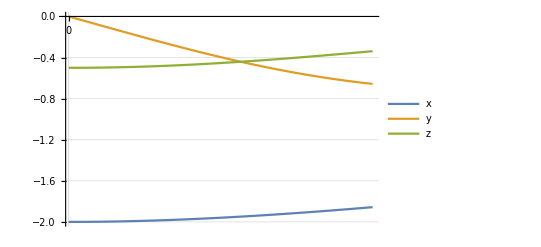
-Graphics-time (s)error(m)

```mathematica
errorp=stateList[[1;;NN,{1,2,3}]]-stateListStar[[1;;NN,{1,2,3}]];
Labeled[
ListLinePlot[{
errorp[[;;,1]],
errorp[[;;,2]],
errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]

(*errorv=stateList[[1;;NN,{13,14,15}]]-stateListStar[[1;;NN,{13,14,15}]];
Labeled[
ListLinePlot[{
errorv[[;;,1]],
errorv[[;;,2]],
errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]*)
```

## Error attitude

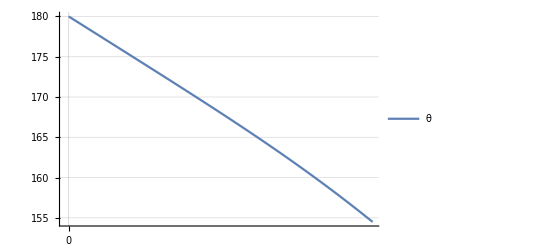
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[
ArcCos[stateList[[i]][[4;;6]].stateListStar[[i]][[4;;6]]] 180/π/.PhysicalConstants,
{i,1,NN}
]
},
PlotLegends->Placed[{"θ"},Above],
Ticks-> {XTicksLabels,Automatic},
PlotRange->Automatic,
GridLines->Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

## Input

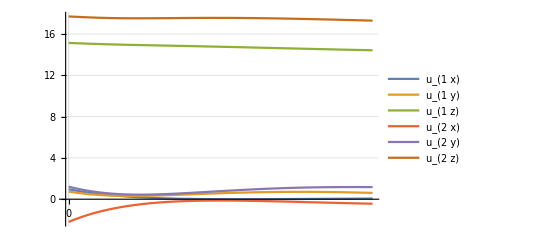
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1],aux[2],aux[3],
aux[4],aux[5],aux[6]
},
PlotLegends->Placed[{"u_(1  x)","u_(1  y)","u_(1  z)","u_(2  x)","u_(2  y)","u_(2  z)"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

## Tensions

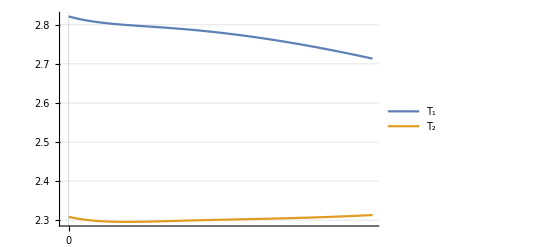
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=tensionsList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1],
aux[2]
},
PlotLegends->Placed[{"T_1","T_2"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

# Attitude Control

## (Augmented) Vector field with attitude

```mathematica
Za[za_,{U1_,U2_,ω1_,ω2_}]:=Join[
Z[za[[1;;24]],Join[U1 r1[za] ,U2 r2[za] ]],
Skew[ω1].r1[za],
Skew[ω2].r2[za]
]
```

## Generate an arbitrary state in the augmented state space

```mathematica
zal[l_]:=Join[zl[l[[1;;18]]],uv3[l[[19;;20]]],uv3[l[[21;;22]]]]
zalR[]=zal[RandomReal[{-1,1},22]];
Timing[Zp[0.1,zalR[]]]
```

{0.,Zp[0.1,{-0.239859,-0.017062,-0.253799,0.86627,0.481686,-0.132496,-0.0399478,0.570648,-0.0371449,-1.07668,-0.513995,0.307751,-0.299887,-0.899451,-0.00182832,0.56749,-0.78705,0.84899,-0.539257,-0.659962,0.525928,-0.394584,-1.06335,-0.586704,0.691565,-0.145709,0.707465,0.603161,-0.433891,0.669279}]}

## Mappings g and h in augmeted state space

```mathematica
ga[za_]:=Join[g[za[[1;;24]]],za[[25;;30]]]
ha[xa_]:=Join[h[xa[[1;;24]]],xa[[25;;30]]]
```

## UAVs attitude in augmented state

```mathematica
r1[za_]:=za[[25;;27]]
r2[za_]:=za[[28;;30]]
```

## Throttle control laws

```mathematica
(*throttle control law UAV 1*)
U1cl[za_,ucl_] := (nC1[za[[1;;12]]].ucl[[1;;3]])/(nC1[za[[1;;12]]].r1[za])/.PhysicalConstants
(*throttle control law UAV 2*)
U2cl[za_,ucl_] := (nC2[za[[1;;12]]].ucl[[4;;6]])/(nC2[za[[1;;12]]].r2[za])/.PhysicalConstants
Ucl[za_,ucl_]:=Join[U1cl[za,ucl]r1[za] ,U2cl[za,ucl]r2[za] ]

(*this is defined for convenience: used in simualtions to compute tensions*)
Uclaux[t_,za_]:=Join[U1cl[za,#]r1[za] ,U2cl[za,#]r2[za] ]&[ucl[t,za[[1;;24]]]]
```

## Vector field Z with chosen throttle control laws

```mathematica
Zp[t_,za_]:=Z[za[[1;;24]],Ucl[za,ucl[t,za[[1;;24]]]]]
```

## Vector field X with chosen throttle control laws

```mathematica
X[{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_,ω1x_,ω1y_,ω1z_,ω2x_,ω2y_,ω2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_},{T1_,T2_,τ1x_,τ1y_,τ1z_,τ2x_,τ2y_,τ2z_}] = Evaluate[D[g[z],{z}]].Z[z,
Join[(nC1[zk].#[[1;;3]])/(nC1[zk].{r1x,r1y,r1z}) {r1x,r1y,r1z},(nC2[zk].#[[4;;6]])/(nC2[zk].{r2x,r2y,r2z}) {r2x,r2y,r2z}]&[ubar[z,{T1,T2,τ1x,τ1y,τ1z,τ2x,τ2y,τ2z}]]
 ]/.Thread[z-> h[x]]/.PhysicalConstants;

Timing[X[Join[xlR[],{0,0,1},{0,0,1}],RandomReal[{-1,1},8]]]
```

{0.492,{0.833037,-0.648376,-0.0150977,-1.06267,-0.746238,-10.9946,-0.269595,-0.068563,-0.263622,6.02091,11.6743,-2.61586,0.0358875,-0.21915,0.0145768,-0.648106,0.136532,0.411832,-1.37361,12.9094,-1.43323,-5.18467,-4.04024,-3.38256}}

## Check the latter vector field (X) has the form we claim

```mathematica
error[{px_,py_,pz_,vx_,vy_,vz_,nx_,ny_,nz_,ωx_,ωy_,ωz_,n1x_,n1y_,n1z_,n2x_,n2y_,n2z_,ω1x_,ω1y_,ω1z_,ω2x_,ω2y_,ω2z_,r1x_,r1y_,r1z_,r2x_,r2y_,r2z_},{T1_,T2_,τ1x_,τ1y_,τ1z_,τ2x_,τ2y_,τ2z_}] =
X[Join[x,{r1x,r1y,r1z}, {r2x,r2y,r2z}],{T1,T2,τ1x,τ1y,τ1z,τ2x,τ2y,τ2z}]-
Join[
v,
(T1  μ1+T2  μ2)/m - gravity{0,0,1},
Skew[ω].n,
(Skew[d1 n].μ1 T1 + Skew[d2 n].μ2  T2)/J,
Skew[ωμ1].μ1,
Skew[ωμ2].μ2,
OP[μ1].({τ1x,τ1y,τ1z}-1/(m1 L1)1/(μ1.{r1x,r1y,r1z})Skew[{r1x,r1y,r1z}].#[[1;;3]]),
OP[μ2].({τ2x,τ2y,τ2z}-1/(m2 L2)1/(μ2.{r2x,r2y,r2z})Skew[{r2x,r2y,r2z}].#[[4;;6]])
]&[ubar[h[x],{T1,T2,τ1x,τ1y,τ1z,τ2x,τ2y,τ2z}]]/.PhysicalConstants;
Chop[error[Join[xlR[],{0,0,1},{0,0,1}],RandomReal[{-1,1},8]]/.PhysicalConstants]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*small relation*)
{dvx,dvy,dvz}.Skew[{rx,ry,rz}].{rxs,rys,rzs}+D[k(1-{rx,ry,rz}.{rxs,rys,rzs}),{{rx,ry,rz,rxs,rys,rzs}}].Join[Skew[{ωxs,ωys,ωzs}+1/k {dvx,dvy,dvz}].{rx,ry,rz}, Skew[{ωxs,ωys,ωzs}].{rxs,rys,rzs}]//Simplify
```

0

#### Derivative of ucl computed in previous section, along vector field Z that includes UAVs attitude

```mathematica
(*too slow the option below*)
(*d1ucl[t_,za_]:=D[ucl[τ,z],Join[{τ},z]].Join[{1},Z[za[[1;;24]],Join[U1cl[t,za]r1[za] ,U2[t,za]r2[za] ]]]/.{τ-> t}/.Thread[z-> za[[1;;24]]]*)
d1ucl[t_,za_]:=(ucl[t+#dt,za[[1;;24]]+#dt Zp[t,za]]-ucl[t,za[[1;;24]]])/(#dt)&[<|"dt"->  0.001|>]
Timing[d1ucl[0.1,zalR[]]]
Timing[d1ucl[0.1,zal[ConstantArray[0,22]]]]
```

{0.188,{-1697.5,-67.8333,-2351.2,-136.231,6.38169,-67.7997}}

{0.212,{-0.219534,-0.674692,-1.12587,-0.25766,-0.930371,-1.3167}}

## control laws for UAVs’ angular velocities (feedforward term + proportional term + backstepping term)

### kVγ must be big, because gradient DωcablesV33[t,xa] is big

```mathematica
ωr1[t_,xa_,u_,du_]:=Skew[u/(√(u.u))].(du/(√(u.u)))+kθAttitude Skew[r1[xa]].(u/(√(u.u)))+1/kVγ(-1/(m1 L1)1/(xa[[13;;15]].r1[xa]))√(u.u) DωcablesV33[t,xa[[1;;24]]][[1;;3]]. OP[xa[[13;;15]]]/.PhysicalConstants/.{kθAttitude-> 15,kVγ-> 200000}
ωr2[t_,xa_,u_,du_]:=Skew[u/(√(u.u))].(du/(√(u.u)))+kθAttitude Skew[r2[xa]].(u/(√(u.u)))+1/kVγ(-1/(m2 L2)1/(xa[[16;;18]].r2[xa]))√(u.u) DωcablesV33[t,xa[[1;;24]]][[4;;6]].OP[xa[[16;;18]]]/.PhysicalConstants/.{kθAttitude-> 15,kVγ-> 200000}
```

## Control law: throttle + angular velocity for each UAV

```mathematica
uacl[t_,za_]:={
(nC1[za[[1;;12]]].(#1[[1;;3]]))/(nC1[za[[1;;12]]].r1[za])/.PhysicalConstants,
(nC2[za[[1;;12]]].(#1[[4;;6]]))/(nC2[za[[1;;12]]].r2[za])/.PhysicalConstants,
ωr1[t,#3,#1[[1;;3]],#2[[1;;3]]],
ωr2[t,#3,#1[[1;;3]],#2[[1;;3]]]
}&[ucl[t,za[[1;;24]]],d1ucl[t,za],ga[za]]
Timing[uacl[0.1,zal[ConstantArray[0,22]]]]
```

{0.424,{15.1332,17.6981,{-0.993166,1.55458,-0.00210874},{-0.847625,0.437513,-0.00210874}}}

## (Augmented) Closed loop vector field

```mathematica
Zacl[t_,za_]:=Za[za,uacl[t,za]]
Timing[Zacl[0.1,zal[ConstantArray[0,22]]]]
```

{0.296,{0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.44978,0.,-5.55112×10^-15,0.,0.,0.,0.44978,0.,0.,0.44978,1.55458,0.993166,0.,0.437513,0.847625,0.}}

## Faster option (without backstepping term)

```mathematica
(*angular velocity control law*)
ωr[r_,u_,du_]:=Skew[u/(√(u.u))].(du/(√(u.u)))+kθAttitude Skew[r].(u/(√(u.u)))/.{kθAttitude-> 20}
(*control law*)
uacl[t_,za_]:={
(nC1[za[[1;;12]]].(#1[[1;;3]]))/(nC1[za[[1;;12]]].r1[za])/.PhysicalConstants,
(nC2[za[[1;;12]]].(#1[[4;;6]]))/(nC2[za[[1;;12]]].r2[za])/.PhysicalConstants,
ωr[r1[za],#1[[1;;3]],#2[[1;;3]]],
ωr[r2[za],#1[[4;;6]],#2[[4;;6]]]
}&[ucl[t,za[[1;;24]]],d1ucl[t,za]]

(*closed loop vector field*)
Zacl[t_,za_]:=Za[za,uacl[t,za]]

(*Timing[uacl[0.1,zarandom]]
Timing[Zacl[0.1,zarandom]]*)
Timing[uacl[0.1,zal[ConstantArray[0,22]]]]
Timing[Zacl[0.1,zal[ConstantArray[0,22]]]]

(*slower option
Zacl[t_,za_]:=Join[
Zp[t,za],
Skew[ωr[r1[za],#1[[1;;3]],#2[[1;;3]]]].r1[za],
Skew[ωr[r2[za],#1[[4;;6]],#2[[4;;6]]]].r2[za]
]&[ucl[t,za[[1;;24]]],d1ucl[t,za]]
Timing[Zacl[0.1,zalR[]]]*)
```

{0.24,{15.1332,17.6981,{-0.854706,1.23037,-0.00210874},{-1.22426,-2.51607,0.00740345}}}

{0.244,{0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.44978,0.,-5.55112×10^-15,0.,0.,0.,0.44978,0.,0.,0.44978,1.23037,0.854706,0.,-2.51607,1.22426,0.}}

## Equilibrium state (x and z)

```mathematica
r1star[t_]:=#/(√(#.#))&[ucl[t,zstar[t]][[1;;3]]]
r2star[t_]:=#/(√(#.#))&[ucl[t,zstar[t]][[4;;6]]]
xastar[t_]:=Join[xstar[t],r1star[t],r2star[t]]
zastar[t_]:=Join[zstar[t],r1star[t],r2star[t]]

Timing[xastar[0.1]]
```

{0.14,{1.99825,0.0837089,0.5,-0.0350461,0.8366,0,-0.999124,-0.0418544,0,0.,0.,0.418667,-0.233426,-0.0097785,0.972325,0.209326,0.0087689,0.977807,0.0950232,0.00398063,0.0228523,-0.0856928,-0.00358977,0.018377,-0.0687528,-0.00390601,0.997626,-0.0141312,-0.00202746,0.999898}}

## Projection operator (take any element in R30 and projects it into Za)

```mathematica
Proja[za_]:=Join[
Proj[za[[1;;24]]],
#/(√(#.#))&[r1[za]],
#/(√(#.#))&[r2[za]]
]/.PhysicalConstants;
Chop[zalR[]-Proja[zalR[]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Simulation

```mathematica
stepsize=0.01;
NN=800;

z0=zal[ConstantArray[0,22]]/.PhysicalConstants;
(*x0=xRandom[]/.PhysicalConstants;*)
stateList={};
stateListStar={};
inputList ={};
tensionsList={};
kk=1;

For[i=1,i<=NN,i++,
time=stepsize(i-1);
zstar0 = zastar[time];
input =uacl[time,z0];
tensions= Te[z0[[1;;24]],Uclaux[time,z0]]/.PhysicalConstants;

stateList= Join[stateList,{z0}];
stateListStar= Join[stateListStar,{zstar0}];
inputList= Join[inputList,{input}];
tensionsList = Join[tensionsList,{tensions}];

zd=  Za[z0,input]/.PhysicalConstants;
z0=Proja[z0+stepsize zd]/.PhysicalConstants;

If[i≥100 kk,Beep[];Print[i];kk=kk+1];
]
```

100

200

300

400

500

600

700

800

900

1000

```mathematica
(*Length[stateList]
Length[stateListStar]
Length[inputList]
Length[tensionsList]*)
```

```mathematica
(*(*continue simulation*)
NN=1300;
For[i=Dimensions[stateList][[1]]+1,i<=NN,i++,
time=stepsize(i-1);
zstar0 = zastar[time];
input =uacl[time,z0];
tensions= Te[z0[[1;;24]],Uclaux[time,z0]]/.PhysicalConstants;

stateList= Join[stateList,{z0}];
stateListStar= Join[stateListStar,{zstar0}];
inputList= Join[inputList,{input}];
tensionsList = Join[tensionsList,{tensions}];

zd=  Za[z0,input]/.PhysicalConstants;
z0=Proja[z0+stepsize zd]/.PhysicalConstants;

If[i≥100 kk,Beep[];Print[i];kk=kk+1];
]*)
```

#### export

```mathematica
Export[NotebookDirectory[]<>"./figures/matlab/data_state.mat",stateList];
Export[NotebookDirectory[]<>"data_state.mx",stateList];
Export[NotebookDirectory[]<>"data_input.mx",inputList];
Export[NotebookDirectory[]<>"data_tensions.mx",tensionsList];
```

#### Import

```mathematica
(*stateList=Import[NotebookDirectory[]<>"data_state.mx"];*)
(*inputList=Import[NotebookDirectory[]<>"data_input.mx"];*)
(*tensionsList=Import[NotebookDirectory[]<>"data_tensions.mx"];*)
```

```mathematica
XTicksLabels={{1,0},{200,2},{400,4},{600,6},{800,8},{1000,10}};
```

## Error position

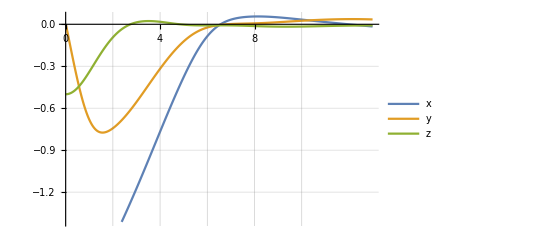
-Graphics-time (s)error(m)

```mathematica
errorp=stateList[[1;;NN,{1,2,3}]]-stateListStar[[1;;NN,{1,2,3}]];
Labeled[
ListLinePlot[{
errorp[[;;,1]],
errorp[[;;,2]],
errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]

(*errorv=stateList[[1;;NN,{13,14,15}]]-stateListStar[[1;;NN,{13,14,15}]];
Labeled[
ListLinePlot[{
errorv[[;;,1]],
errorv[[;;,2]],
errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]*)
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_error_position.pdf",%];
```

## Error attitude

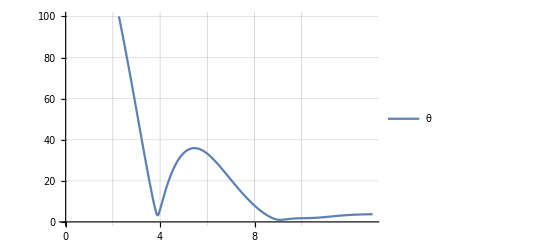
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[ArcCos[stateList[[i]][[4;;6]].stateListStar[[i]][[4;;6]]] 180/π,{i,1,NN}]
},
PlotLegends->Placed[{"θ"},Above],
Ticks-> {XTicksLabels,Automatic},
PlotRange->{0,100},
GridLines->Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_error_attitude.pdf",%];
```

## Error attitude in UAV

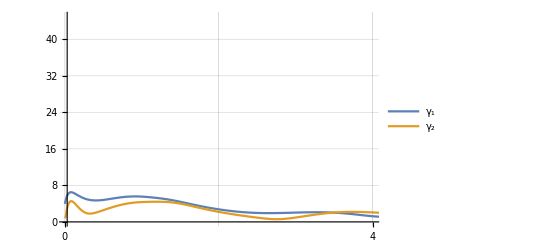
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[ArcCos[r1[stateList[[i]]].r1[stateListStar[[i]]]] 180/π,{i,1,NN}],
Table[ArcCos[r2[stateList[[i]]].r2[stateListStar[[i]]]] 180/π,{i,1,NN}]
},
PlotLegends->Placed[{"γ_1","γ_2"},Above],
Ticks-> {XTicksLabels,Automatic},
PlotRange->{{2,4/stepsize},{0,45}},
GridLines->Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_uavs_attitude_error.pdf",%];
```

## Error attitude COMBINED

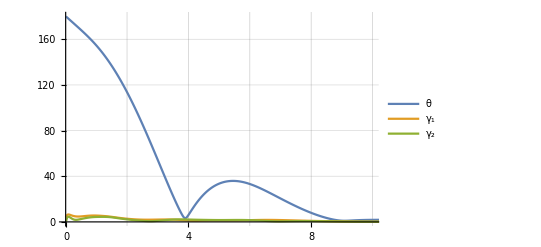
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[ArcCos[stateList[[i]][[4;;6]].stateListStar[[i]][[4;;6]]] 180/π,{i,1,NN}],
Table[ArcCos[r1[stateList[[i]]].r1[stateListStar[[i]]]] 180/π,{i,1,NN}],
Table[ArcCos[r2[stateList[[i]]].r2[stateListStar[[i]]]] 180/π,{i,1,NN}]
},
PlotLegends->Placed[{"θ","γ_1","γ_2"},Above],
Ticks-> {XTicksLabels,Automatic},
PlotRange->{{0,10/stepsize},{0,180}},
GridLines->Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_attitude_error_combined.pdf",%];
```

## Input

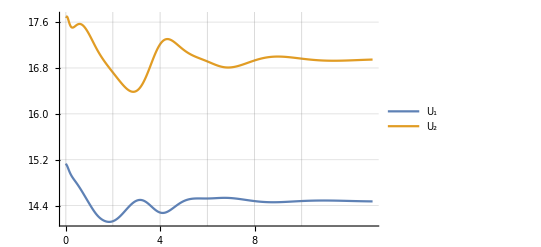
-Graphics-time (s)Thrust(N)

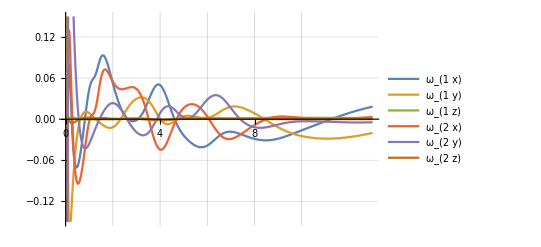
-Graphics-time (s)Angular velocities(hz)

```mathematica
aux[comp_]:=inputList[[;;]][[comp]]
Labeled[
ListLinePlot[{
Table[inputList[[i]][[1]],{i,1,NN}],
Table[inputList[[i]][[2]],{i,1,NN}]
},
PlotLegends->Placed[{"U_1","U_2"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","Thrust(N)"},{Bottom,Left},RotateLabel->True
]
Export[NotebookDirectory[]<>"figures/sim_uavs_thrusts.pdf",%];
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
Table[inputList[[i]][[3]][[1]],{i,1,NN}],
Table[inputList[[i]][[3]][[2]],{i,1,NN}],
Table[inputList[[i]][[3]][[3]],{i,1,NN}],
Table[inputList[[i]][[4]][[1]],{i,1,NN}],
Table[inputList[[i]][[4]][[2]],{i,1,NN}],
Table[inputList[[i]][[4]][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"ω_(1  x)","ω_(1  y)","ω_(1  z)","ω_(2  x)","ω_(2  y)","ω_(2  z)"},Above],
PlotRange->{-0.15,0.15},
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","Angular velocities(hz)"},{Bottom,Left},RotateLabel->True
]
Export[NotebookDirectory[]<>"figures/sim_uavs_angular_velocities.pdf",%];
```

## Tensions

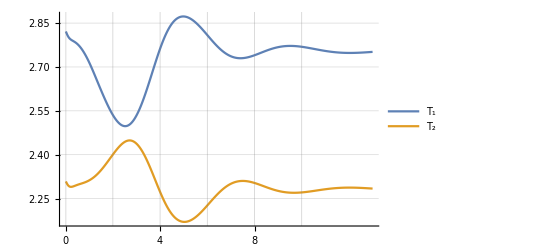
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=tensionsList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1],
aux[2]
},
PlotLegends->Placed[{"T_1","T_2"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_tensions.pdf",%];
```